# Solving the S and T-Equations by guessing κ

```mathematica
<<utils`
```

```mathematica
$PlotTheme="Scientific";
```

```mathematica
sEquation=(-κ-k^2/σ^2+β σ^2+γ σ^4) S[σ]+S'[σ]/σ+S''[σ]==0
tEquation=(κ-k^2/τ^2+β τ^2-γ τ^4) T[τ]+T'[τ]/τ+T''[τ]==0
```

(-κ-k^2/σ^2+β σ^2+γ σ^4) S[σ]+S'[σ]/σ+S''[σ]==0

(κ-k^2/τ^2+β τ^2-γ τ^4) T[τ]+T'[τ]/τ+T''[τ]==0

### Find sData

Generating the data points takes about a minute!

```mathematica
Solve[1/Sqrt[2a]==2Sqrt[Subscript[R, 0]],a]
```

{{a→1/(8 R_0)}}

```mathematica
Module[{sBoundary,sInterpolationBoundary,zero,consts,sEquationWithConsts,lowerLim,upperLim},
sBoundary=2;
sInterpolationBoundary=4;
zero=0.00000001;
consts={k->0,γ->1};
sEquationWithConsts=sEquation//.consts;
{lowerLim,upperLim}={-15,15};
sData0 = Table[
{κκ,β/.utils`shootingMethod[{sEquationWithConsts/.κ->κκ,S[zero]==1,S'[zero]==0},S,{σ,zero,sInterpolationBoundary},{β,-120}, sBoundary][[1]]},
{κκ,lowerLim, upperLim}];
sData1 = Table[
{κκ,β/.utils`shootingMethod[{sEquationWithConsts/.κ->κκ,S[zero]==1,S'[zero]==0},S,{σ,zero,sInterpolationBoundary},{β,sData0[[κκ-lowerLim+1,2]]+1.}, sBoundary][[1]]},
{κκ,lowerLim, upperLim}];
sData2= Table[
{κκ,β/.utils`shootingMethod[{sEquationWithConsts/.κ->κκ,S[zero]==1,S'[zero]==0},S,{σ,zero,sInterpolationBoundary},{β,sData1[[κκ-lowerLim+1,2]]+1.}, sBoundary][[1]]},
{κκ,lowerLim, upperLim}];
]
```

### Find tData

```mathematica
Module[{tInterpolationBoundary,zero,consts,tEquationWithConsts,lowerLim,upperLim},
tInterpolationBoundary=4;
zero=0.00000001;
consts={k->0,γ->1};
tEquationWithConsts=tEquation//.consts;
{lowerLim,upperLim}={-15,15};
tData0 = Table[
{κκ,β/.utils`shootingMethod[{tEquationWithConsts/.κ->κκ,T[zero]==1,T'[zero]==0},T,{τ,zero,tInterpolationBoundary},{β,-70}, None][[1]]},
{κκ,lowerLim,upperLim}];
tData1 =Table[
{κκ,β/.utils`shootingMethod[{tEquationWithConsts/.κ->κκ,T[zero]==1,T'[zero]==0},T,{τ,zero,tInterpolationBoundary},{β,tData0[[κκ-lowerLim+1,2]]+.1}, None][[1]]},
{κκ,lowerLim,upperLim}];
tData2 =Table[
{κκ,β/.utils`shootingMethod[{tEquationWithConsts/.κ->κκ,T[zero]==1,T'[zero]==0},T,{τ,zero,tInterpolationBoundary},{β,tData1[[κκ-lowerLim+1,2]]+.1}, None][[1]]},
{κκ,lowerLim,upperLim}];]
```

### Plot and Fit

```mathematica
βS0Fit=Interpolation[sData0];
βS1Fit=Interpolation[sData1];
βS2Fit=Interpolation[sData2];
```

```mathematica
βT0Fit=Interpolation[tData0];
βT1Fit=Interpolation[tData1];
βT2Fit=Interpolation[tData2];
```

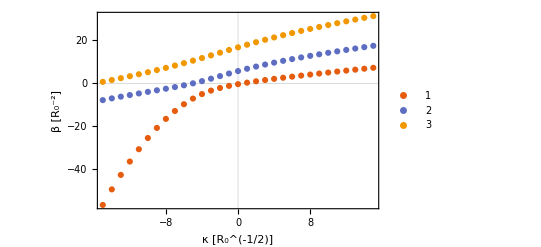

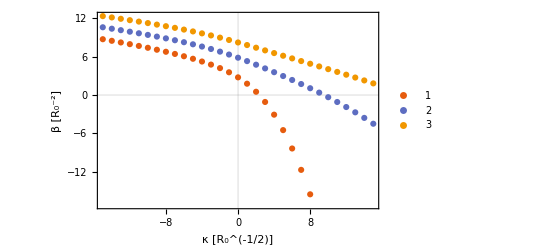

```mathematica
ListPlot[{sData0, sData1,sData2}, PlotLegends->Automatic, FrameLabel->{"κ [R_0^(-1/2)]","β [R_0^-2]"}, PlotRange->Full]
ListPlot[{tData0, tData1,tData2}, PlotLegends->Automatic, FrameLabel->{"κ [R_0^(-1/2)]","β [R_0^-2]"}]
```

### Visualize intersections in plot

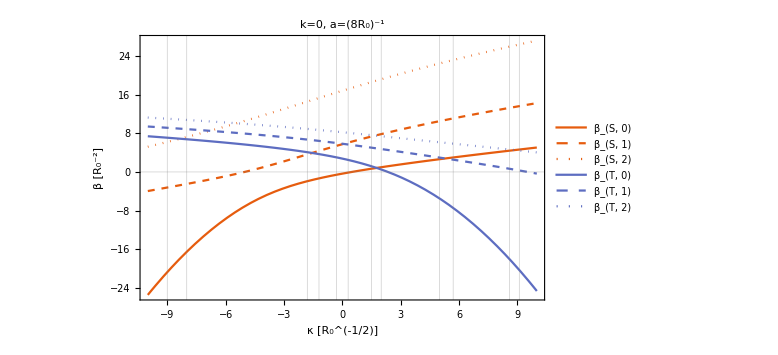

```mathematica
vlines={-9,-8,-1.8,-1.2,-0.3, 0.3,1.5,2,5,5.7,8.6,9.1};
Plot[{βS0Fit[κ],βS1Fit[κ],βS2Fit[κ],βT0Fit[κ],βT1Fit[κ],βT2Fit[κ]},{κ,-10,10},PlotStyle->Tuples[{{RGBColor[0.9, 0.36, 0.054],RGBColor[0.365248, 0.427802, 0.758297]},{Automatic,Dashed,Dotted}}],  FrameLabel->{"κ [R_0^(-1/2)]","β [R_0^-2]"},PlotLabel->"k=0, a=(8R_0)^-1",PlotLegends->{"β_(S, 0)","β_(S, 1)","β_(S, 2)","β_(T, 0)","β_(T, 1)","β_(T, 2)"},ImageSize->Large,GridLines->{vlines,{0}}]
```

### Vary κ to find κ_(m,n) and β_(m,n)

```mathematica
Module[{tInterpolationBoundary,sInterpolationBoundary,sBoundary,energies,brentIntervals,zero,consts,tEquationWithConsts,sEquationWithConsts,βSSol,βTSol,κSol},
tInterpolationBoundary=4;
sInterpolationBoundary=4;
sBoundary=2;
energies=SetPrecision[{.1,.1,4,.1,.1,4},15];
brentIntervals=SetPrecision[Partition[vlines,2],15];
zero=0.00000001`15;
consts={k->0,γ->1`15};
tEquationWithConsts=tEquation//.consts;
sEquationWithConsts=sEquation//.consts;
βTSol[κκ_Real,β0_Real]:=utils`shootingMethod[{tEquationWithConsts/.κ->κκ,T[zero]==1,T'[zero]==0},T,{τ,zero,tInterpolationBoundary},{β, β0},None,"Output"->"Value","Precision"->10][[1]];
βSSol[κκ_Real,β0_Real]:=utils`shootingMethod[{sEquationWithConsts/.κ->κκ,S[zero]==1,S'[zero]==0},S,{σ, zero, sInterpolationBoundary},{β,β0},sBoundary,"Output"->"Value","Precision"->10][[1]];
κSol=FindRoot[βTSol[κ,#[[1]]]-βSSol[κ,#[[1]]],{κ,#[[2]],#[[3]]},MaxIterations->100,WorkingPrecision->15,PrecisionGoal->10,Method->"Brent"]&/@(Join[Partition[energies,1],brentIntervals,2]);
{κ,βTSol[κ,β0]}/.Partition[Riffle[((β0->#)&/@energies),Flatten[κSol]],2]
];
κβValues=SortBy[SetPrecision[%,10],Last](*Sort by increasing energy*)
```

{{1.764931082,0.8320429299},{5.293697216,2.783981809},{-1.554409948,3.923653664},{8.865291609,4.519689437},{0.05874915096,5.795839318},{-8.34183454,6.864002975}}

Define some labels:

```mathematica
βNames={Subscript[β, 0,0],Subscript[β, 0,1],Subscript[β, 1,0],Subscript[β, 0,2],Subscript[β, 1,1],Subscript[β, 2,0]};
sNames={Subscript[S, 0,0][σ],Subscript[S, 0,1][σ],Subscript[S, 1,0][σ],Subscript[S, 0,2][σ],Subscript[S, 1,1][σ],Subscript[S, 2,0][σ]};
tNames={Subscript[T, 0,0][τ],Subscript[T, 0,1][τ],Subscript[T, 1,0][τ],Subscript[T, 0,2][τ],Subscript[T, 1,1][τ],Subscript[T, 2,0][τ]};
```

Plot κβvalues in onto fit curves to see wether the results make sense

```mathematica
g1=Plot[{βS0Fit[κ],βS1Fit[κ],βS2Fit[κ],βT0Fit[κ],βT1Fit[κ],βT2Fit[κ]},{κ,-10,10},PlotStyle->Tuples[{{RGBColor[0.9, 0.36, 0.054],RGBColor[0.365248, 0.427802, 0.758297]},{Automatic,Dashed,Dotted}}],  FrameLabel->{"κ R_0^(1/2)","β R_0^2"},PlotLabel->"k=0, a=(8R_0)^-1",PlotLegends->{Subscript[β, S,0][κ],Subscript[β, S,1][κ],Subscript[β, S,2][κ],Subscript[β, T,0][κ],Subscript[β, T,1][κ],Subscript[β, T,2][κ]},ImageSize->Large,LabelStyle->Larger];
g2=ListPlot[κβValues->βNames,PlotStyle->{PointSize[Large],Opacity[.5,Black]},LabelStyle->Larger];
Show[g1,g2]
```

-Graphics-

### Plot Eigenstates

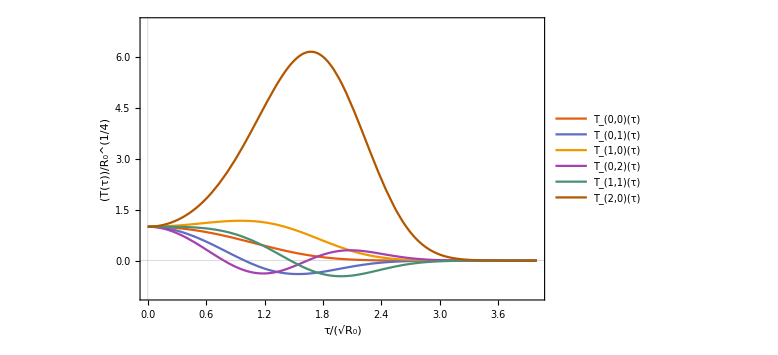
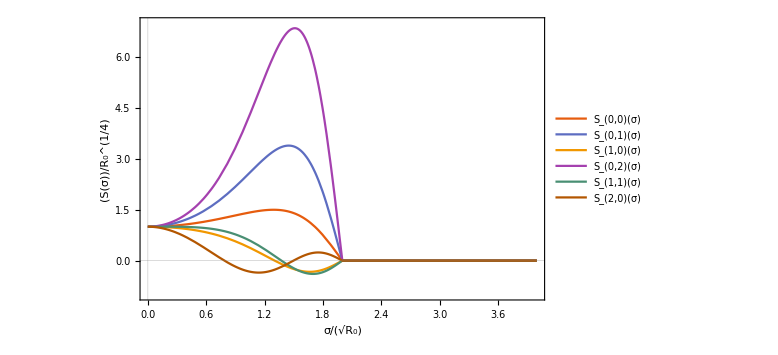

```mathematica
Module[{tInterpolationBoundary,sInterpolationBoundary,sBoundary,zero,consts,tEquationWithConsts,sEquationWithConsts,sSol,tSol,κSol,g1,g2},
tInterpolationBoundary=4;
sInterpolationBoundary=4;
sBoundary=2;
zero=0.00000001`15;
consts={k->0,γ->1`15};
tEquationWithConsts=tEquation//.consts;
sEquationWithConsts=sEquation//.consts;
tSol[{κκ_Real,ββ_Real}]:=First@NDSolve[{tEquationWithConsts/.{κ->κκ,β->ββ},T[zero]==1,T'[zero]==0},T[τ],{τ,zero,tInterpolationBoundary}];
sSol[{κκ_Real,ββ_Real}]:=First@NDSolve[{sEquationWithConsts/.{κ->κκ,β->ββ},S[zero]==1,S'[zero]==0},S[σ],{σ,zero,sInterpolationBoundary}];
g1=Plot[Evaluate[T[τ]/.(tSol/@κβValues)[[;;6]]],{τ,0,tInterpolationBoundary},PlotRange->{Full,{-1,7}},ImageSize->Large,LabelStyle->Larger,PlotLegends->tNames,FrameLabel->{τ/Sqrt[Subscript[R, 0]],T[τ] Subscript[R, 0]^(-1/4)},PlotTheme->"Scientific"];
g2=Plot[Evaluate[S[σ]Boole[σ<sBoundary]/.(sSol/@κβValues)[[;;6]]],{σ,0,sInterpolationBoundary},PlotRange->{Full,{-1,7}},ImageSize->Large,LabelStyle->Larger,PlotLegends->sNames,FrameLabel->{σ/Sqrt[Subscript[R, 0]],S[σ] Subscript[R, 0]^(-1/4)},PlotTheme->"Scientific"];
{g1,g2}
]
```

```mathematica
Module[{tInterpolationBoundary,sInterpolationBoundary,sBoundary,zero,consts,tEquationWithConsts,sEquationWithConsts,sSol,tSol,κSol,g1,g2},
tInterpolationBoundary=4;
sInterpolationBoundary=4;
sBoundary=2;
zero=0.00000001`15;
consts={k->0,γ->1`15};
tEquationWithConsts=tEquation//.consts;
sEquationWithConsts=sEquation//.consts;
tSol[{κκ_Real,ββ_Real}]:=First@NDSolve[{tEquationWithConsts/.{κ->κκ,β->ββ},T[zero]==1,T'[zero]==0},T[τ],{τ,zero,tInterpolationBoundary}];
sSol[{κκ_Real,ββ_Real}]:=First@NDSolve[{sEquationWithConsts/.{κ->κκ,β->ββ},S[zero]==1,S'[zero]==0},S[σ],{σ,zero,sInterpolationBoundary}];
(*g1=Plot[Evaluate[T[τ]/.(tSol/@κβValues)],{τ,0,tInterpolationBoundary},PlotRange->{Full,{-1,8}},ImageSize->Large,LabelStyle->Large,PlotLegends->tNames,FrameLabel->{τ/Sqrt[Subscript[R, 0]],T[τ] Subscript[R, 0]^(-1/4)}];
g2=Plot[Evaluate[S[σ]Boole[σ<sBoundary]/.(sSol/@κβValues)],{σ,0,sInterpolationBoundary},PlotRange->{Full,{-1,8}},ImageSize->Large,LabelStyle->Large,PlotLegends->sNames,FrameLabel->{σ/Sqrt[Subscript[R, 0]],S[σ] Subscript[R, 0]^(-1/4)}];*)
(*{g1,g2}*)
{tSol/@κβValues,tNames}
]
```

{{{T[τ]→InterpolatingFunction[…][τ]},{T[τ]→InterpolatingFunction[…][τ]},{T[τ]→InterpolatingFunction[…][τ]},{T[τ]→InterpolatingFunction[…][τ]},{T[τ]→InterpolatingFunction[…][τ]},{T[τ]→InterpolatingFunction[…][τ]}},{T_(0,0)[τ],T_(0,1)[τ],T_(1,0)[τ],T_(0,2)[τ],T_(1,1)[τ],T_(2,0)[τ]}}

### Convert β to energy

```mathematica
βToΕ[a_,Ε0_,R0_,β_]:=(Ε0 (1+2 a R0^3 β))/(4 a R0)
κβValues[[;;,2]]
βNames
```

{0.8320429299,2.783981809,3.923653664,4.519689437,5.795839318,6.864002975}

{β_(0,0),β_(0,1),β_(1,0),β_(0,2),β_(1,1),β_(2,0)}

```mathematica
βToΕ[a,Ε0,R0,#/R0^2]&/@κβValues[[;;,2]]//.{a->1/(8R0),Ε0->Quantity[7.58029746*^-13, "Electronvolts"],R0->Quantity[7.39400728*^-6, "Meters"]}
```

{1.83142×10^-12 eV,2.57123×10^-12 eV,3.00318×10^-12 eV,3.22909×10^-12 eV,3.71277×10^-12 eV,4.11762×10^-12 eV}

```mathematica
QuantityMagnitude@{Quantity[1.8314161373929937*^-12, "Electronvolts"],Quantity[2.5712300038935898*^-12, "Electronvolts"],Quantity[3.003182587193448*^-12, "Electronvolts"],Quantity[3.2290890099971362*^-12, "Electronvolts"],Quantity[3.712768794864952*^-12, "Electronvolts"],Quantity[4.117618707815927*^-12, "Electronvolts"]}*1*^12
```

{1.83142,2.57123,3.00318,3.22909,3.71277,4.11762}